# Reading the Record: Analysis, Inference, and Feedback in Continuous Quantum Measurement

## A computation-first sequel to Watching a Qubit. We keep exactly the same readout map ℛ and positivity-preserving trajectory map 𝒯, then ask what can be learned or controlled from the numbers a detector actually returns. Built-in Wolfram Language functions expose correlations, spectra, and changing frequencies; the same conditional update reconstructs a state from an external record; a likelihood turns innovations into parameter estimates; and record feedback closes the loop. The Function Repository's LindbladSolve supplies independent master-equation references, exactly as it did in the companion chapter.

Mads Bahrami. Last updated July 31, 2026.

### Setting the Stage: From a Trajectory to a Data Analysis

The companion chapter, Watching a Qubit: Continuous Measurement and Quantum Trajectories, built two objects. The readout map ℛ produces one vector of detector increments, and the trajectory map 𝒯 uses those increments to propagate the conditional state. That chapter used the record mainly to explain where a trajectory comes from. Here the record becomes the main object of study.

The distinction to hold onto is simple: the detector returns increments d y_n, not a density matrix. The current J_n=d y_n/dt is a rescaled view of the same data. A conditional state, a spectral peak, a parameter estimate, and a feedback command are all computations made from that stream.

In other words, there is one raw object and several questions we can ask of it:

Question | Record calculation | What it can tell us
Does the record remember its past? | CorrelationFunction | Oscillation and decay scales
Which frequencies persist? | PeriodogramArray or PowerSpectralDensity | Resonances and noise floor
Does the frequency change with time? | SpectrogramArray | Nonstationary dynamics
What state is consistent with the readings? | The conditional update inside 𝒯 | Filtered state
Which model best predicts the readings? | LogLikelihood of the innovations | Parameter estimate
Can the readings steer the system? | Measurement followed by a record-dependent unitary | Feedback control

I strongly believe in a computation-first narrative for learning: in a sense, if I cannot compute it, I cannot claim to understand it. Each section therefore makes one physical claim, computes it, and checks it against either synthetic shot noise, a replay of the same record, or an independent master-equation calculation.

This is a live Wolfram notebook. Evaluate it from top to bottom in a fresh kernel because later cells depend on earlier ones. The narrative is a continuous sequence, like a movie: read each output and its physical meaning before studying every detail of the input. You are not locked into the baseline parameters. Once the notebook runs, change the drive, rate, step, record length, and random seed, then ask which conclusions survive. Questions and corrections are welcome through the repository that contains this lesson.

### Prerequisites and How to Read This

The prerequisites are the companion chapter, basic density matrices, and the distinction between a Wiener increment of variance dt and a current sample of variance 1/dt. We use ℏ=1 throughout. The pace steepens in the likelihood and feedback parts, but each new layer still begins from the same two maps. The long-record cells take more time than the short examples because frequency resolution is bought with observation time. My suggestion is to focus on what each output establishes before worrying about every implementation detail.

The code uses plain complex matrices and built-in Wolfram Language functions. Like the companion chapter, it calls ResourceFunction["LindbladSolve"] for deterministic master-equation references. The resource installs automatically on first use, so that first evaluation may need a network connection.

Let's start!

## Part I: Preserve the Record Contract

The source of truth is the companion chapter. Its readout convention is

d y_(r,n)=√η_r Tr[(L_r+L_r^†)ρ_n]dt+d W_(r,n),    d W_(r,n)∼𝒩(0,dt).

In other words, ℛ returns one increment per monitored channel, while 𝒯 returns the list of conditional states and Sows those increments as a side effect.

Copy the two definitions without refactoring them so this notebook and the companion cannot silently adopt different update rules:

```mathematica
ClearAll[ℛ, 𝒯];
ℛ[ρ_, Ls_, dt_, dw_, η_] :=
   MapThread[Sqrt[#3] Tr[(#1 + ConjugateTranspose[#1]) . ρ] dt + #2 &, {Ls, dw, η}];

𝒯[ρ0_?MatrixQ, H_?MatrixQ, Ls_List, η : (None | _List) : None,
   V : (None | _List) : None, dt_?NumericQ, tf_?NumericQ] :=
  Module[
   {d = Length[ρ0], r0 = N[ρ0], Hn = N[H], Lsn = N[Ls], dtn = N[dt],
    ηv, Vsn, heff, lcorr, nsteps, dw, step},
   ηv = N[If[η === None, ConstantArray[1, Length[Ls]], η]];
   Vsn = If[V === None, {}, N[V]];
   heff = IdentityMatrix[d] - dtn (I Hn
       + (1/2) Total[ConjugateTranspose[#] . # & /@ Lsn]
       + (1/2) Total[ConjugateTranspose[#] . # & /@ Vsn]);
   lcorr = (dtn/2) Total[MapThread[#1 (#2 . #2) &, {ηv, Lsn}]];
   nsteps = Floor[tf/dt];
   dw = Transpose[RandomVariate[NormalDistribution[0, Sqrt[dtn]], {Length[Lsn], nsteps}]];
   step[ρ_, dwv_] := Module[{dy, s, m, num},
      dy = Sow[ℛ[ρ, Lsn, dtn, dwv, ηv]];
      s = Total[MapThread[#1 Sqrt[#2] #3 &, {dy, ηv, Lsn}]];
      m = heff + s + (1/2) s . s - lcorr;
      num = m . ρ . ConjugateTranspose[m]
          + dtn Total[(# . ρ . ConjugateTranspose[#]) & /@ Vsn]
          + dtn Total[MapThread[(1 - #2) (#1 . ρ . ConjugateTranspose[#1]) &, {Lsn, ηv}]];
      num/Tr[num]];
   FoldList[step, r0, dw]];
```

This is the one deliberately dense cell in the lesson. It is infrastructure copied from the companion, not a new idea compressed into code.

Now choose the same matrix conventions as the companion. The lowering operator sends the excited basis vector 0 to the ground basis vector 1:

```mathematica
X = PauliMatrix[1]; Y = PauliMatrix[2]; Z = PauliMatrix[3];
Jminus = (X - I Y)/2;
{Jminus . {1, 0}, Jminus . {0, 1}}
```

{{0,1},{0,0}}

A state vector still needs to become a density matrix. Define that conversion, a Bloch-vector reader, and one reusable density-operator test explicitly:

```mathematica
ClearAll[densityMatrix, blochVector, densityOperatorQ];
densityMatrix[ψ_] := Outer[Times, ψ, Conjugate[ψ]];
blochVector[ρ_] := Re[Tr[ρ . #] & /@ {X, Y, Z}];
densityOperatorQ[ρ_?MatrixQ] :=
 Max[Abs@Flatten[ρ - ConjugateTranspose[ρ]]] < 10^-10 &&
  Abs[Tr[ρ] - 1] < 10^-10 &&
  Min[Re@Eigenvalues[(ρ + ConjugateTranspose[ρ])/2]] > -10^-10;
```

We need a long, approximately stationary record. Drive an emitting qubit on resonance and let the transient occupy only a small fraction of the run:

```mathematica
Ω0 = 3.5; γ0 = 0.7; dt0 = 0.01; tf0 = 1200.;
H0 = Ω0 Y/2; L0 = {Sqrt[γ0] Jminus};
ρ0 = densityMatrix[{1, 0}];
{HermitianMatrixQ[H0], densityOperatorQ[ρ0]}
```

{True,True}

The two checks confirm that the numerical experiment starts from a Hermitian Hamiltonian and a Hermitian, unit-trace, positive state.

Generate the conditional states and reap the readout increments:

```mathematica
{trajectory0, {record0}} = BlockRandom[
   SeedRandom[1]; Reap@𝒯[ρ0, H0, L0, dt0, tf0]
   ];
```

There is one monitored channel, so pull out its increments and build the corresponding current:

```mathematica
dy0 = Re@record0[[All, 1]];
current0 = dy0/dt0;
```

Check the scale before analyzing anything:

```mathematica
<|"samples" -> Length[dy0],
  "increment standard deviation" -> StandardDeviation[dy0],
  "Wiener scale" -> Sqrt[dt0],
  "current standard deviation" -> StandardDeviation[current0]|>
```

<|samples→120000,increment standard deviation→0.100017,Wiener scale→0.1,current standard deviation→10.0017|>

The increment fluctuates on the √dt scale, while the current fluctuates on the 1/√dt scale. This is the first guardrail: filtering and likelihood consume dy0; a spectrum may use either dy0 or current0, but its normalization must say which one it uses.

## Part II: Correlation Before Spectrum

A correlation asks whether two samples separated by a lag tend to move together. The built-in CorrelationFunction subtracts the sample mean and normalizes by the variance, so it reports a dimensionless autocorrelation rather than the raw covariance.

In other words, the zero-lag shot-noise spike is scaled to one, and coherent dynamics appear as much smaller oscillations at nonzero lag.

Compute the correlation from one step out to eight time units, skipping every fourth lag to keep the plot light:

```mathematica
lagSteps = Range[1, Floor[8/dt0], 4];
corr0 = CorrelationFunction[dy0, {First[lagSteps], Last[lagSteps], 4}];
```

Plot it against physical lag rather than sample number:

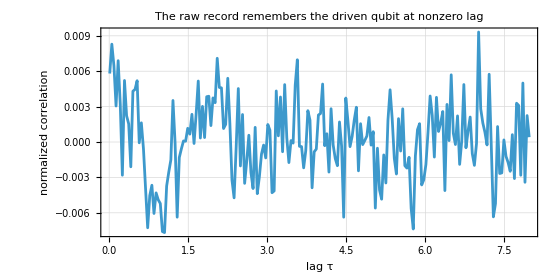

```mathematica
ListLinePlot[Transpose[{dt0 lagSteps, corr0}],
 Frame -> True, GridLines -> Automatic, ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"lag τ", "normalized correlation"},
 PlotLabel -> "The raw record remembers the driven qubit at nonzero lag"]
```

The oscillation is the qubit, but its amplitude is smaller than individual finite-record fluctuations. Confirm first that the same estimator applied to a pure Wiener record also has nonzero sample scatter:

```mathematica
pureDy = BlockRandom[
   SeedRandom[2]; RandomVariate[NormalDistribution[0, Sqrt[dt0]], Length[dy0]]
   ];
pureCorr = CorrelationFunction[pureDy, {First[lagSteps], Last[lagSteps], 4}];
Max[Abs[pureCorr]]
```

0.00924111

The maxima are similar, so the largest correlation value alone cannot identify the qubit. We need a statistic chosen from the model before comparing the two records. The Hamiltonian fixes the trial oscillation scale at Ω_0, so project both correlations onto that cosine before comparing either score:

```mathematica
correlationTemplate = Cos[Ω0 dt0 lagSteps];
correlationScores =
  (# . correlationTemplate/Norm[correlationTemplate] &) /@ {corr0, pureCorr};
AssociationThread[{"qubit record", "pure Wiener record"}, correlationScores]
```

<|qubit record→0.0125618,pure Wiener record→-0.00122969|>

As one can see, the model-guided oscillatory score separates these seeded records even though their largest individual correlation values do not. This is still a demonstration, not a detection threshold. A serious claim needs independent seeds or a sampling distribution for the score.

## Part III: A Calibrated Power Spectrum with Built-in Functions

The Wiener-Khinchin theorem connects the covariance to the power spectral density. For the normalized homodyne current

J_n=(d y_n)/dt,

white shot noise has a flat two-sided spectral density equal to one. Since PeriodogramArray preserves the mean power per sample, the physical normalization can be written in either of two equivalent ways:

S_J(ω_k)=dt PeriodogramArray[J]_k=1/dt PeriodogramArray[dy]_k.

In other words, the factor of dt is a units conversion, not an adjustable constant.

Choose overlapping segments and a Hann window. The overlap averages more estimates, while the window reduces leakage from a frequency that does not land exactly on a discrete Fourier bin:

```mathematica
nWindow = 8192; nOffset = nWindow/2; nFourier = nWindow;
periodogram0 = PeriodogramArray[
    dy0 - Mean[dy0], nWindow, nOffset, HannWindow, nFourier
    ]/dt0;
```

Verify directly that analyzing the current gives the same normalized array:

```mathematica
currentPeriodogram = dt0 PeriodogramArray[
    current0 - Mean[current0], nWindow, nOffset, HannWindow, nFourier
    ];
Max[Abs[currentPeriodogram - periodogram0]] < 10^-12
```

True

Attach the physical angular-frequency axis and retain the nonnegative half. We keep the two-sided normalization, so the shot-noise floor remains one even though only one half is plotted:

```mathematica
nPositive = Floor[nFourier/2] + 1;
ωGrid = 2 Pi Range[0, nPositive - 1]/(nFourier dt0);
spectrum0 = Transpose[{ωGrid, periodogram0[[1 ;; nPositive]]}];
```

Calibrate the estimator on synthetic shot noise before interpreting the qubit:

```mathematica
noisePeriodogram = PeriodogramArray[
    pureDy - Mean[pureDy], nWindow, nOffset, HannWindow, nFourier
    ]/dt0;
Mean[noisePeriodogram]
```

1.00026

The result is close to one. The same conclusion can be checked at a chosen angular frequency with PowerSpectralDensity, whose smoothing specification is a cutoff together with a window:

```mathematica
PowerSpectralDensity[
  pureDy - Mean[pureDy], Ω0 dt0, {512, HannWindow}
  ]/dt0
```

0.973339

PowerSpectralDensity is convenient when a symbolic frequency or a few selected frequencies are wanted. PeriodogramArray is convenient when a dense grid and explicit segment averaging are wanted. Both are built-in, and neither requires us to write a Fourier normalization by hand.

Now plot the measured spectrum over the band containing the drive:

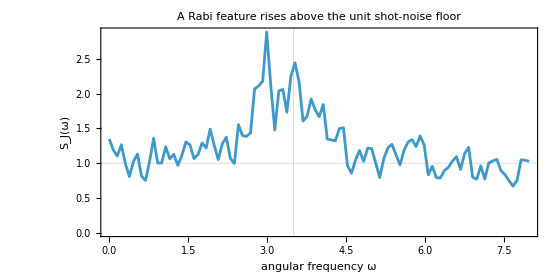

```mathematica
ListLinePlot[Select[spectrum0, First[#] <= 8 &],
 Frame -> True, GridLines -> {{Ω0}, {1}}, PlotRange -> All,
 ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"angular frequency ω", "S_J(ω)"},
 PlotLabel -> "A Rabi feature rises above the unit shot-noise floor"]
```

One raw bin is a poor frequency estimator for a broad noisy line. Instead, subtract the calibrated unit floor, clip negative finite-sample fluctuations to zero, and compute the excess-power centroid inside a search band chosen before looking at the noise outside it. The estimator must also handle a record with no power above the floor:

```mathematica
ClearAll[excessPowerCentroid];
excessPowerCentroid[spectrum_List, {ωmin_, ωmax_}, floor_: 1] := Module[
  {band = Select[spectrum, ωmin < First[#] < ωmax &], weights},
  If[band === {},
   Return[Failure["NoSpectralFeature",
     <|"MessageTemplate" -> "The selected band is empty."|>]]];
  weights = Clip[band[[All, 2]] - floor, {0, Infinity}];
  If[Total[weights] > 0,
   Total[band[[All, 1]] weights]/Total[weights],
   Failure["NoSpectralFeature",
    <|"MessageTemplate" -> "The selected band has no power above the floor."|>]
   ]
  ];
```

Apply the guarded estimator to the record and verify its no-feature boundary:

```mathematica
featureFrequency = excessPowerCentroid[spectrum0, {2, 5}];
<|"excess-power centroid" -> featureFrequency,
  "drive parameter" -> Ω0,
  "Fourier-bin width" -> 2 Pi/(nFourier dt0),
  "flat unit spectrum rejected" ->
    FailureQ@excessPowerCentroid[{{2.5, 1.}, {3.5, 1.}}, {2, 5}]|>
```

<|excess-power centroid→3.38339,drive parameter→3.5,Fourier-bin width→0.076699,flat unit spectrum rejected→True|>

As one can see, the centroid locates the coherent oscillation scale without pretending that one upward noise fluctuation is the line center. Its uncertainty is limited by record length, linewidth, band choice, and the estimator itself. It would be too strong to say that this one number gives the Hamiltonian exactly, or that the full width is always equal to the bare emission rate.

### The Deterministic Reference: Use the Companion's LindbladSolve

The record spectrum reveals an oscillation scale in noisy detector data. An independent check should use the same Hamiltonian and collapse operator without reusing the stochastic trajectory update. The companion chapter already chose ResourceFunction["LindbladSolve"] for exactly this job.

Solve the unconditional master equation over a short transient:

```mathematica
lindblad0 = ResourceFunction["LindbladSolve"][
    H0, L0, ρ0, {t, 0, 6.}
    ];
```

Sample the deterministic X expectation on the same time step as the record:

```mathematica
lindbladTimes = Range[0., 6., dt0];
lindbladX = blochVector[lindblad0[#]][[1]] & /@ lindbladTimes;
```

Plot the transient before reducing it to one number:

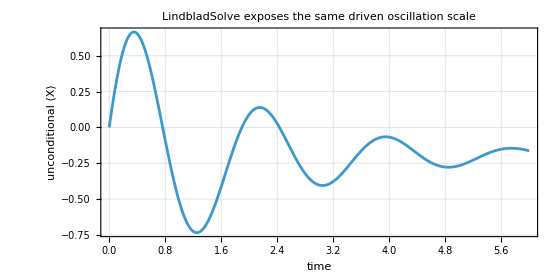

```mathematica
ListLinePlot[Transpose[{lindbladTimes, lindbladX}],
 Frame -> True, GridLines -> Automatic, ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"time", "unconditional ⟨X⟩"},
 PlotLabel -> "LindbladSolve exposes the same driven oscillation scale"]
```

The local maxima are separated by one oscillation period. Use the built-in FindPeaks and convert the mean peak spacing to an angular frequency:

```mathematica
lindbladPeakIndices = FindPeaks[lindbladX][[All, 1]];
lindbladPeakTimes = lindbladTimes[[lindbladPeakIndices]];
lindbladFrequency = 2 Pi/Mean[Differences[lindbladPeakTimes]];
```

Compare the noisy record estimate with the independent deterministic estimate:

```mathematica
<|"record excess-power centroid" -> featureFrequency,
  "Lindblad peak-spacing frequency" -> lindbladFrequency,
  "agreement within 0.5" -> Abs[featureFrequency - lindbladFrequency] < 0.5|>
```

<|record excess-power centroid→3.38339,Lindblad peak-spacing frequency→3.49066,agreement within 0.5→True|>

As one can see, the two calculations locate the same dynamical scale. They do not compute the same object: one is a stationary detector-record spectrum, while the other is an unconditional transient. Agreement in frequency is therefore a consistency check, not a derivation of the full measured spectrum.

This distinction also prevents a common overstatement. The Mollow triplet is normally the spectrum of the emitted field's first-order correlation. A homodyne-current spectrum is quadrature resolved, so it should not be called a Mollow triplet without computing the appropriate field correlation and its weights.

### Nonstationary Records: When One Spectrum Is Not Enough

A periodogram averages over the whole record and therefore assumes that its statistics are approximately stationary. If a drive changes halfway through the experiment, the global spectrum mixes the two regimes.

In other words, ask a time-frequency question with a time-frequency function.

Generate two consecutive record segments with different Rabi frequencies, carrying the final state of the first segment into the second:

```mathematica
{trajectorySlow, {recordSlow}} = BlockRandom[
   SeedRandom[11]; Reap@𝒯[ρ0, 2.0 Y/2, L0, dt0, 250.]
   ];
{trajectoryFast, {recordFast}} = BlockRandom[
   SeedRandom[12]; Reap@𝒯[Last[trajectorySlow], 5.0 Y/2, L0, dt0, 250.]
   ];
switchedDy = Join[Re@recordSlow[[All, 1]], Re@recordFast[[All, 1]]];
```

Use SpectrogramArray for the short-time Fourier transform, then average neighboring time windows to make a persistent line easier to distinguish from shot noise:

```mathematica
nSTFT = 2048; hop = 256;
stftPower = MovingAverage[
   Abs[SpectrogramArray[switchedDy - Mean[switchedDy], nSTFT, hop, HannWindow]]^2,
   15
   ];
maxFrequencyBin = Floor[8 nSTFT dt0/(2 Pi)] + 1;
```

Plot only the physical frequency band of interest:

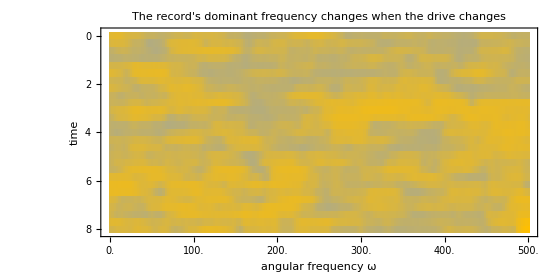

```mathematica
MatrixPlot[
 Transpose@Log10[10^-10 + stftPower[[All, 1 ;; maxFrequencyBin]]],
 DataRange -> {{0, Length[switchedDy] dt0}, {0, 8}}, DataReversed -> True,
 ColorFunction -> (Blend[{StandardBlue, StandardYellow}, #] &),
 Frame -> True, ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"time", "angular frequency ω"},
 PlotLabel -> "The record's dominant frequency changes when the drive changes"]
```

The picture is suggestive, but we should compute the change rather than read it only by eye. Average the first and second halves of the spectrogram and locate the strongest line in a fixed band:

```mathematica
stftFrequencies = 2 Pi Range[0, maxFrequencyBin - 1]/(nSTFT dt0);
stftBand = Flatten@Position[stftFrequencies, ω_ /; 1 < ω < 7];
halfSpectra = Mean /@ Partition[stftPower, Floor[Length[stftPower]/2]][[1 ;; 2]];
halfFeatureFrequencies = Function[halfSpectrum,
     stftFrequencies[[stftBand[[First@Ordering[halfSpectrum[[stftBand]], -1]]]]]
     ] /@ halfSpectra;
AssociationThread[{"first half", "second half"}, halfFeatureFrequencies]
```

<|first half→1.84078,second half→4.90874|>

Verify that the two computed features lie near the imposed drive values:

```mathematica
Max[Abs[halfFeatureFrequencies - {2., 5.}]] < 0.3
```

True

The time-frequency calculation resolves the switch for this seeded record. It sacrifices frequency resolution to recover timing. That tradeoff is unavoidable: longer windows locate frequency more sharply, while shorter windows locate a change more sharply.

Before we move on, let us summarize the most important points we have learned so far:

dy0 fluctuates on the √dt scale, while current0 fluctuates on the 1/√dt scale.

A model-guided projection separates the qubit's oscillatory correlation from a pure Wiener record, while the largest raw correlation value does not.

PeriodogramArray[dy]/dt and dt PeriodogramArray[current] share a unit white-noise floor.

An excess-power centroid finds a broad Rabi feature without overinterpreting a single raw bin.

SpectrogramArray and the two half-record estimates resolve the imposed change from 2 to 5.

LindbladSolve gives an independent unconditional transient whose peak spacing agrees with the record's oscillation scale.

## Part IV: Replay an External Record as a Quantum Filter

The trajectory generator draws dW, converts it to dy with ℛ, and then updates the state. An experiment supplies dy directly. Filtering therefore removes only the random draw and keeps the state update unchanged.

In other words, the following functions do not define a second trajectory algorithm. They validate the external record, expose the body of 𝒯 after the line that generated the record, then fold the supplied values through the same s, m, and num expressions.

First check the physical dimensions: a positive time step, a density operator and Hermitian Hamiltonian of the same size, at least one compatible monitored channel, one efficiency per channel, and one numeric entry per channel in every record row:

```mathematica
ClearAll[validRecordModelQ];
validRecordModelQ[ρ0_, H_, Ls_List, η_, V_, dt_, record_List] := Module[
  {d = Length[ρ0], Vs = If[V === None, {}, V]},
  TrueQ[dt > 0] && densityOperatorQ[N[ρ0]] && HermitianMatrixQ[N[H]] &&
   Dimensions[H] == {d, d} && Length[Ls] > 0 &&
   AllTrue[Join[Ls, Vs], MatrixQ[#] && Dimensions[#] == {d, d} &] &&
   (η === None || (ListQ[η] && Length[η] == Length[Ls] &&
      VectorQ[η, Function[x, NumberQ[N[x]] && TrueQ[0 <= x <= 1]]])) &&
   AllTrue[record, Function[row,
     Length[row] == Length[Ls] &&
      VectorQ[row, Function[x, NumberQ[N[x]] && TrueQ[Abs[Im[N[x]]] < 10^-10]]]]]
  ];
```

Now build the one-step update from the unchanged coefficients of 𝒯:

```mathematica
ClearAll[makeConditionedStep];
makeConditionedStep[ρ0_?MatrixQ, H_?MatrixQ, Ls_List, η_, V_, dt_?NumericQ] :=
 Module[{d = Length[ρ0], Hn = N[H], Lsn = N[Ls], dtn = N[dt],
   ηv, Vsn, heff, lcorr},
  ηv = N[If[η === None, ConstantArray[1, Length[Ls]], η]];
  Vsn = If[V === None, {}, N[V]];
  heff = IdentityMatrix[d] - dtn (I Hn
      + (1/2) Total[ConjugateTranspose[#] . # & /@ Lsn]
      + (1/2) Total[ConjugateTranspose[#] . # & /@ Vsn]);
  lcorr = (dtn/2) Total[MapThread[#1 (#2 . #2) &, {ηv, Lsn}]];
  Function[{ρ, dy}, Module[{s, m, num},
    s = Total[MapThread[#1 Sqrt[#2] #3 &, {dy, ηv, Lsn}]];
    m = heff + s + (1/2) s . s - lcorr;
    num = m . ρ . ConjugateTranspose[m]
       + dtn Total[(# . ρ . ConjugateTranspose[#]) & /@ Vsn]
       + dtn Total[MapThread[(1 - #2) (#1 . ρ . ConjugateTranspose[#1]) &, {Lsn, ηv}]];
    num/Tr[num]]]
  ];
```

Now fold that step through an external record:

```mathematica
ClearAll[conditionOnRecord];
conditionOnRecord[ρ0_, H_, Ls_, dt_, record_] :=
 conditionOnRecord[ρ0, H, Ls, None, None, dt, record];
conditionOnRecord[ρ0_, H_, Ls_, η_, dt_, record_] :=
 conditionOnRecord[ρ0, H, Ls, η, None, dt, record];
conditionOnRecord[ρ0_, H_, Ls_, η_, V_, dt_, record_] :=
 If[TrueQ@validRecordModelQ[ρ0, H, Ls, η, V, dt, record],
  Module[{step = makeConditionedStep[ρ0, H, Ls, η, V, dt]},
   FoldList[step, N[ρ0], N[record]]
   ],
  Failure["InvalidRecordModel",
   <|"MessageTemplate" -> "Dimensions, efficiencies, or record rows are incompatible."|>]
  ];
```

The strongest implementation check is a round trip. Generate a short trajectory, retain its record, and replay that record from the same initial state:

```mathematica
{trajectoryReplay, {recordReplay}} = BlockRandom[
   SeedRandom[20]; Reap@𝒯[ρ0, H0, L0, dt0, 8.]
   ];
filteredReplay = conditionOnRecord[ρ0, H0, L0, dt0, recordReplay];
Max[Abs@Flatten[trajectoryReplay - filteredReplay]]
```

0.

The difference should be zero to machine precision. This is stronger than saying the two curves look similar: the filter and generator use the same increments and the same update.

The definitions are list based, so a one-channel example should not be their only test. Generate a short record from simultaneous monitored X and Z channels, replay both columns, and challenge the validator with malformed inputs:

```mathematica
LTwo = {Sqrt[0.2] X, Sqrt[0.3] Z}; ηTwo = {0.7, 0.5};
{trajectoryTwo, {recordTwo}} = BlockRandom[
   SeedRandom[22]; Reap@𝒯[ρ0, 0. X, LTwo, ηTwo, dt0, 0.2]
   ];
filteredTwo = conditionOnRecord[ρ0, 0. X, LTwo, ηTwo, dt0, recordTwo];
<|"record dimensions" -> Dimensions[recordTwo],
  "two-channel replay error" -> Max[Abs@Flatten[trajectoryTwo - filteredTwo]]|>
```

<|record dimensions→{20,2},two-channel replay error→0.|>

As expected, the record has two columns and its replay error vanishes. Now challenge the validator with misaligned efficiencies, the wrong number of columns, a complex increment, and symbolic efficiencies:

```mathematica
<|"short efficiency list rejected" ->
    FailureQ@conditionOnRecord[ρ0, 0. X, LTwo, {0.7}, dt0, recordTwo],
  "one-column record rejected" ->
    FailureQ@conditionOnRecord[ρ0, 0. X, LTwo, ηTwo, dt0, recordTwo[[All, {1}]]],
  "complex record rejected" -> FailureQ@conditionOnRecord[
    ρ0, 0. X, LTwo, ηTwo, dt0, ReplacePart[recordTwo, {1, 1} -> I]],
  "symbolic efficiencies rejected" ->
    FailureQ@conditionOnRecord[ρ0, 0. X, LTwo, {ηx, ηz}, dt0, recordTwo]|>
```

<|short efficiency list rejected→True,one-column record rejected→True,complex record rejected→True,symbolic efficiencies rejected→True|>

Alignment errors, complex increments, and symbolic efficiencies all return a Failure instead of entering the numerical update.

Now start the replay from a wrong prior. Inefficient detection keeps the true conditional state mixed, which makes trace distance a more informative comparison than raw overlap:

```mathematica
ηWrong = {0.6};
{trajectoryWrong, {recordWrong}} = BlockRandom[
   SeedRandom[21]; Reap@𝒯[ρ0, H0, L0, ηWrong, dt0, 10.]
   ];
filteredWrong = conditionOnRecord[
   IdentityMatrix[2]/2, H0, L0, ηWrong, dt0, recordWrong
   ];
```

Compute the trace distance at every step:

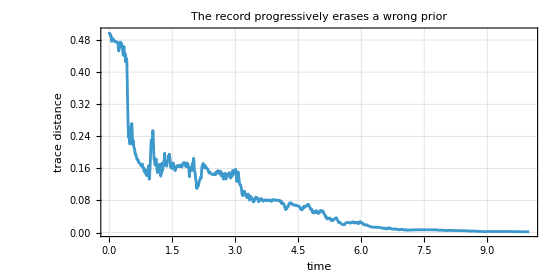

```mathematica
traceDistances = MapThread[
   Total[Abs@Eigenvalues[#1 - #2]]/2 &,
   {trajectoryWrong, filteredWrong}
   ];
ListLinePlot[Transpose[{dt0 Range[0, Length[traceDistances] - 1], traceDistances}],
 Frame -> True, GridLines -> Automatic, PlotRange -> {0, All},
 ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"time", "trace distance"},
 PlotLabel -> "The record progressively erases a wrong prior"]
```

For an observable and stable filter, the distance tends to shrink as the shared record accumulates. It need not decrease at every individual step, and not every measurement model identifies every component of the state. Prior forgetting is a property to test for the chosen dynamics, not a universal monotonicity theorem.

Check Hermiticity, unit trace, and positivity together over the generated and reconstructed states:

```mathematica
AllTrue[
 Join[trajectoryReplay, filteredReplay, trajectoryTwo, filteredTwo,
  trajectoryWrong, filteredWrong], densityOperatorQ]
```

True

## Part V: Estimate a Parameter from the Innovations

A candidate model predicts a conditional mean for each next increment. For independent homodyne channels,

d y_n|ρ_n∼𝒩(μ_n,dt I),    (μ_n)_r=√η_r Tr[(L_r+L_r^†)ρ_n]dt.

The difference d y_n-μ_n is the innovation. A good candidate makes the observed innovations probable; a poor candidate leaves structured residuals.

In other words, parameter estimation is repeated filtering plus a built-in Gaussian log likelihood.

Define the record likelihood for any number of independent monitored channels:

```mathematica
ClearAll[recordLogLikelihood];
recordLogLikelihood[ρ0_, H_, Ls_, η_List, V_, dt_, record_] :=
 Module[{trajectory, means, observations, innovations},
  trajectory = conditionOnRecord[ρ0, H, Ls, η, V, dt, record];
  means = Function[ρ,
      MapThread[
       Sqrt[#2] Re@Tr[(#1 + ConjugateTranspose[#1]) . ρ] dt &,
       {Ls, η}
       ]
      ] /@ Most[trajectory];
  observations = Re@N[record];
  innovations = Flatten[observations - means];
  LogLikelihood[NormalDistribution[0, Sqrt[dt]], innovations]
  ];
```

The flattening step must preserve channel alignment. Reuse the two-channel record to compute its innovation matrix explicitly:

```mathematica
twoChannelMeans = Function[ρ,
     MapThread[
      Sqrt[#2] Re@Tr[(#1 + ConjugateTranspose[#1]) . ρ] dt0 &,
      {LTwo, ηTwo}]
     ] /@ Most[filteredTwo];
twoChannelInnovations = Re@recordTwo - twoChannelMeans;
Dimensions[twoChannelInnovations]
```

{20,2}

Now verify that the multichannel function equals the explicit sum of the scalar Gaussian log densities:

```mathematica
twoChannelLikelihood = recordLogLikelihood[
   ρ0, 0. X, LTwo, ηTwo, None, dt0, recordTwo];
explicitTwoChannelLikelihood = Total[
   Log[PDF[NormalDistribution[0, Sqrt[dt0]], #]] & /@
    Flatten[twoChannelInnovations]];
Abs[twoChannelLikelihood - explicitTwoChannelLikelihood] < 10^-10
```

True

Generate a finite record at a known drive. Keep the record much shorter than the spectral example so that the finite-data uncertainty remains visible:

```mathematica
ΩTrue = 1.7; γEstimate = 0.8; ηEstimate = {0.7};
HEstimate = ΩTrue X; LEstimate = {Sqrt[γEstimate] Jminus};
recordEstimate = BlockRandom[
   SeedRandom[31];
   Reap@𝒯[ρ0, HEstimate, LEstimate, ηEstimate, dt0, 60.]
   ][[2, 1]];
```

Scan candidate drives. A grid makes the entire likelihood landscape visible, including secondary structure or a boundary maximum that a single optimizer call could hide:

```mathematica
ΩCandidates = Range[1.2, 2.2, 0.1];
logLikelihoodFull = recordLogLikelihood[
      ρ0, # X, LEstimate, ηEstimate, None, dt0, recordEstimate
      ] & /@ ΩCandidates;
relativeFull = logLikelihoodFull - Max[logLikelihoodFull];
```

Compare the full record with its first third:

```mathematica
shortRecord = Take[recordEstimate, Floor[Length[recordEstimate]/3]];
logLikelihoodShort = recordLogLikelihood[
      ρ0, # X, LEstimate, ηEstimate, None, dt0, shortRecord
      ] & /@ ΩCandidates;
relativeShort = logLikelihoodShort - Max[logLikelihoodShort];
```

Plot both profiles and mark the generating value:

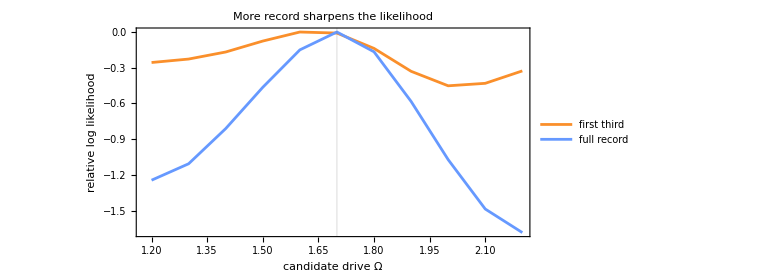

```mathematica
ListLinePlot[
 {Transpose[{ΩCandidates, relativeShort}], Transpose[{ΩCandidates, relativeFull}]},
 PlotStyle -> {StandardOrange, Directive[Thick, StandardBlue]},
 PlotLegends -> {"first third", "full record"}, GridLines -> {{ΩTrue}, None},
 Frame -> True, ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"candidate drive Ω", "relative log likelihood"},
PlotLabel -> "More record sharpens the likelihood"]
```

As one can see, the full-record profile is narrower around its maximum than the first-third profile. The longer record therefore discriminates nearby drive values more strongly.

Read off the grid maximum only after seeing the profile:

```mathematica
ΩEstimate = First@First@MaximalBy[
    Transpose[{ΩCandidates, logLikelihoodFull}], Last
    ];
<|"estimate" -> ΩEstimate, "generating value" -> ΩTrue|>
```

<|estimate→1.7,generating value→1.7|>

The word sharper should also name a computed criterion. Use the centered second difference at each profile maximum: a more negative value means greater local curvature on this common grid:

```mathematica
ClearAll[peakCurvature];
peakCurvature[values_List] := Module[{i = First@Ordering[values, -1]},
  If[1 < i < Length[values],
   values[[i + 1]] - 2 values[[i]] + values[[i - 1]], Indeterminate]
  ];
profileCurvatures = peakCurvature /@ {relativeShort, relativeFull};
<|"first-third curvature" -> First[profileCurvatures],
  "full-record curvature" -> Last[profileCurvatures],
  "full record is sharper" ->
    Abs[Last[profileCurvatures]] > Abs[First[profileCurvatures]]|>
```

<|first-third curvature→-0.0849687,full-record curvature→-0.316452,full record is sharper→True|>

A finite record can move the maximum away from the generating value. That is sampling uncertainty, not automatically a coding error. A serious inference should also refine the grid, examine the innovations, and report an interval from likelihood curvature, bootstrap records, or Fisher information rather than only the maximizing number.

Before we move on, let us summarize the most important points we have learned so far:

makeConditionedStep contains the same s, m, and num update as 𝒯, with no new random draw.

Replaying one-channel and two-channel records from the same prior reproduces both original trajectories to machine precision.

A filter started from the maximally mixed prior approaches the reference conditional state for this observable example.

Each candidate drive produces a sequence of innovations d y_n-μ_n with variance dt.

The two-channel likelihood equals the explicit sum of all per-channel Gaussian log densities.

LogLikelihood ranks those innovation sequences, and the full record gives a sharper profile than its first third.

## Part VI: Close the Loop with the Same Trajectory Map

For unit-efficiency Markovian feedback, let a Hermitian operator F_r multiply each measured current. During one step, the current produces the unitary kick

U_(fb,n)=exp [-i∑_r F_r d y_(r,n)].

The order matters. First 𝒯 performs one measurement step and produces dy; then the record from that same step determines the unitary.

In other words, feedback can wrap 𝒯 one step at a time without introducing another SME implementation. One Hermitian feedback operator is required for each monitored channel; otherwise the proposed kick is not the unitary controller just described.

Check that physical input condition before building the wrapper:

```mathematica
ClearAll[validFeedbackOperatorsQ];
validFeedbackOperatorsQ[ρ0_?MatrixQ, H_?MatrixQ, Ls_List, Fs_List] :=
 densityOperatorQ[N[ρ0]] && Dimensions[ρ0] == Dimensions[H] &&
  Length[Ls] > 0 && Length[Ls] == Length[Fs] && HermitianMatrixQ[N[H]] &&
  AllTrue[Fs, HermitianMatrixQ] &&
  AllTrue[Join[Ls, Fs], MatrixQ[#] && Dimensions[#] == Dimensions[H] &];
```

Test one physical controller and five invalid specifications:

```mathematica
<|"physical controller" -> validFeedbackOperatorsQ[ρ0, 0. X, {Z}, {Y}],
  "non-Hermitian operator" -> validFeedbackOperatorsQ[ρ0, 0. X, {Z}, {Jminus}],
  "wrong channel count" -> validFeedbackOperatorsQ[ρ0, 0. X, {Z}, {Y, Y}],
  "empty channel list" -> validFeedbackOperatorsQ[ρ0, 0. X, {}, {}],
  "wrong state dimension" ->
    validFeedbackOperatorsQ[IdentityMatrix[3]/3, 0. X, {Z}, {Y}],
  "non-density initial matrix" ->
    validFeedbackOperatorsQ[2 ρ0, 0. X, {Z}, {Y}]|>
```

<|physical controller→True,non-Hermitian operator→False,wrong channel count→False,empty channel list→False,wrong state dimension→False,non-density initial matrix→False|>

The valid Hermitian controller passes. Non-Hermitian, misaligned, empty, wrong-dimension, and non-density specifications do not. Build the unit-efficiency wrapper only for a valid initial state, channel list, and operator list:

```mathematica
ClearAll[feedbackTrajectory];
feedbackTrajectory[ρ0_, H_, Ls_, Fs_, dt_, tf_] :=
 If[TrueQ[NumberQ[N[dt]] && NumberQ[N[tf]] && dt > 0 && tf >= 0 &&
    validFeedbackOperatorsQ[ρ0, H, Ls, Fs]],
  Module[{step},
   step[ρ_] := Module[{measured, oneRecord, dy, u},
     {measured, {oneRecord}} = Reap@𝒯[ρ, H, Ls, dt, dt];
     dy = First[oneRecord];
     Sow[dy];
     u = MatrixExp[-I Total[MapThread[#1 #2 &, {dy, Fs}]]];
     u . Last[measured] . ConjugateTranspose[u]
     ];
   NestList[step, N[ρ0], Floor[tf/dt]]
   ],
  Failure["InvalidFeedbackModel",
   <|"MessageTemplate" -> "Use nonempty aligned channels and Hermitian feedback operators."|>]
  ];
```

Confirm that the wrapper itself returns a structured failure for the non-Hermitian controller:

```mathematica
FailureQ@feedbackTrajectory[ρ0, 0. X, {Z}, {Jminus}, dt0, 0.1]
```

True

Choose a transparent control problem. Continuously measure Z with c=√k Z and feed the record back through F=√k Y. In the continuous-time, zero-delay limit the ensemble master equation is

ρ̇=-i[H+1/2(c^†F+Fc),ρ]+𝒟[c-iF]ρ.

Here c^†F+Fc=0, and c-iF=√k(Z-iY) has the +1 eigenstate of X as a dark state. The feedback should therefore stabilize +x from an initially mixed state.

Verify both parts of that statement symbolically before choosing a numerical rate:

```mathematica
ketPlusX = {1, 1}/Sqrt[2];
FullSimplify[
 (Sqrt[κ] (Z - I Y)).ketPlusX == {0, 0} &&
  X.ketPlusX == ketPlusX,
 Assumptions -> κ > 0]
```

True

Set the controller and run an ensemble:

```mathematica
kFeedback = 0.8; dtFeedback = 0.01; tfFeedback = 2.;
HFeedback = 0. X;
LFeedback = {Sqrt[kFeedback] Z};
FFeedback = {Sqrt[kFeedback] Y};
ρMixed = IdentityMatrix[2]/2;
ensembleFeedback = BlockRandom[
   SeedRandom[41];
   Table[feedbackTrajectory[
     ρMixed, HFeedback, LFeedback, FFeedback, dtFeedback, tfFeedback
     ], {80}]
   ];
```

Build the independent deterministic reference with the same LindbladSolve used in the companion chapter:

```mathematica
cFeedback = First[LFeedback]; fFeedback = First[FFeedback];
hWisemanMilburn = HFeedback
   + (ConjugateTranspose[cFeedback] . fFeedback + fFeedback . cFeedback)/2;
jumpWisemanMilburn = cFeedback - I fFeedback;
referenceFeedback = ResourceFunction["LindbladSolve"][
   hWisemanMilburn, {jumpWisemanMilburn}, ρMixed, {t, 0, tfFeedback}
   ];
```

{{0.,0.},{0.,0.}}

Compare the ensemble mean with the deterministic curve:

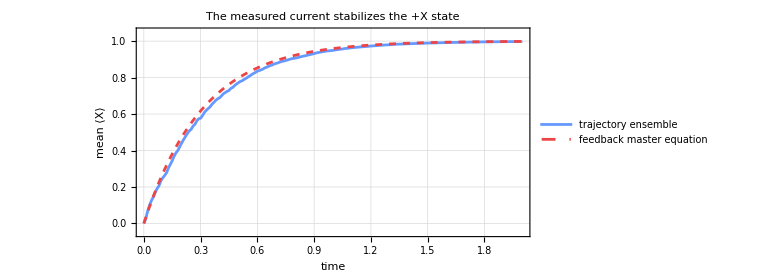

```mathematica
timeFeedback = dtFeedback Range[0, Floor[tfFeedback/dtFeedback]];
meanFeedback = Mean[ensembleFeedback];
xMeanFeedback = blochVector[#][[1]] & /@ meanFeedback;
xReferenceFeedback = blochVector[referenceFeedback[#]][[1]] & /@ timeFeedback;
ListLinePlot[
 {Transpose[{timeFeedback, xMeanFeedback}],
  Transpose[{timeFeedback, xReferenceFeedback}]},
 PlotStyle -> {Directive[Thick, StandardBlue], Directive[Dashed, StandardRed]},
 PlotLegends -> {"trajectory ensemble", "feedback master equation"},
 Frame -> True, GridLines -> Automatic, PlotRange -> {-0.05, 1.05},
 ImageSize -> 560, AspectRatio -> 1/2,
 FrameLabel -> {"time", "mean ⟨X⟩"},
 PlotLabel -> "The measured current stabilizes the +X state"]
```

Both curves approach ⟨X⟩=1: the trajectory ensemble and the independent LindbladSolve reference agree that the feedback stabilizes the +X state.

The displayed difference contains both finite-step error and Monte Carlo error. Without rerunning the trajectories, compare the root-mean-square discrepancy for several nested ensemble sizes:

```mathematica
ClearAll[feedbackRMS];
feedbackRMS[n_Integer?Positive] /; n <= Length[ensembleFeedback] := Module[{xMean},
  xMean = blochVector[#][[1]] & /@ Mean[Take[ensembleFeedback, n]];
  Sqrt[Mean[(xMean - xReferenceFeedback)^2]]
  ];
ensembleCounts = {5, 10, 20, 40, 60, 80};
AssociationThread[ensembleCounts, feedbackRMS /@ ensembleCounts]
```

<|5→0.043863,10→0.025855,20→0.016809,40→0.00791116,60→0.0102736,80→0.0170348|>

As one can see, the discrepancy initially falls and then fluctuates rather than decreasing monotonically for every nested subset. That is itself a useful Monte Carlo lesson: one seed is not a convergence proof. A production study should average the error over independent seeds and repeat the calculation for smaller values of dtFeedback.

Finally check agreement at the combined discretization and Monte Carlo scale, and positivity of a representative conditioned run:

```mathematica
<|"maximum ensemble-reference difference" ->
    Max[Abs[xMeanFeedback - xReferenceFeedback]],
  "Monte Carlo scale" -> 1/Sqrt[Length[ensembleFeedback]],
  "maximum difference is below that scale" ->
    Max[Abs[xMeanFeedback - xReferenceFeedback]] <
     1/Sqrt[Length[ensembleFeedback]],
  "representative run remains a density operator" ->
    AllTrue[First[ensembleFeedback], densityOperatorQ]|>
```

<|maximum ensemble-reference difference→0.0407777,Monte Carlo scale→1/(4 √5),maximum difference is below that scale→True,representative run remains a density operator→True|>

The unitary kick preserves positivity exactly. The numerical comparison above tests one finite step and one seeded ensemble; it is not a substitute for a full convergence scan. Finite delay, inefficient detection, filtering bandwidth, and actuator saturation require an enlarged control model; the unit-efficiency, zero-delay formula should not be used for them without modification.

## Part VII: What the Record Does Not Give for Free

The calculations above support several sharp boundaries.

The lesson has deliberately covered distinct regimes rather than treating one seeded trajectory as universal:

Regime | Evidence computed here
General symbolic case | Fully symbolic stochastic paths are not meaningful because the detector record is a numerical random draw. The general list structure is still exercised by the two-channel replay, and the feedback dark-state identity retains symbolic κ.
Exactly solvable special case | The symbolic dark-state calculation proves $(c-iF)
Limiting case | A pure Wiener record gives a unit spectral floor and a much smaller matched oscillatory score for the seeded comparison.
Numerical reference case | Replay, likelihood recovery, spectrogram switching, and the feedback master-equation comparison provide independent numeric checks.
Failure or edge case | A band with no excess spectral power, misaligned records and efficiencies, complex records, symbolic efficiencies, invalid initial states, feedback lists, non-Hermitian controllers, and empty controllers are rejected; low periodogram bins, reversed-record filtering, and field-spectrum labels are ruled out as shortcuts.

First, a low periodogram bin is not evidence of squeezing. A noisy periodogram fluctuates above and below its expectation even for vacuum noise. Squeezing requires a calibrated quadrature spectrum, uncertainty estimates, and a statistically significant band below the unit floor. Taking Min of one realization is biased downward and cannot establish it.

Second, a spectral peak is not automatically a Mollow triplet. The measured observable and its correlation function decide the weights. The unconditional LindbladSolve transient can confirm a shared dynamical frequency, but it does not determine the weights in a field spectrum.

Third, filtering is not smoothing. conditionOnRecord is causal: the state at step n uses records only through step n. A genuine quantum smoother combines a forward conditional state with a backward effect or an equivalent past-quantum-state construction. Reversing the record through the forward filter is not that construction. In a linear-Gaussian limit, Wolfram Language's KalmanEstimator supplies the classical forward analogue, but a classical Rauch-Tung-Striebel example should be labeled as an analogy rather than as a quantum smoother.

Fourth, feedback is a physical loop, not just a post-processing curve. Its delay, efficiency convention, and bandwidth enter the dynamics. The wrapper above states its regime explicitly: unit efficiency, negligible delay, one measurement step followed by one unitary kick.

These boundaries are useful because they tell us what computation must come next. To claim squeezing, add statistical error bars or independent records. To identify a field spectrum, compute the correct two-time operator correlation. To smooth a quantum estimate, add the backward effect. To model an experiment's feedback, add its delay and efficiency.

## Where This Leaves Us (and What Comes Next)

We began with exactly the ℛ and 𝒯 of the companion chapter and did not create a competing trajectory implementation. From their Sowed increments we computed a correlation with CorrelationFunction, a calibrated spectrum with PeriodogramArray and PowerSpectralDensity, and a changing frequency with SpectrogramArray. The companion's LindbladSolve then supplied an independent unconditional transient with the same oscillation scale.

The same update then became a filter by replacing generated noise with an external record. A round trip proved that replaying a generated record reconstructs the generated trajectory. Built-in LogLikelihood turned the filter's innovations into a parameter profile. Finally, wrapping one call to 𝒯 per step closed a unit-efficiency feedback loop, and LindbladSolve supplied the independent Wiseman-Milburn master-equation reference.

The next useful extensions are now precise rather than aspirational: multichannel cross-spectra, likelihood-based joint estimation with uncertainty, a backward-effect quantum smoother, and delayed or inefficient feedback. Each begins from the same record contract. The detector produces dy; everything else is an inference or an action built from it.

### References and Acknowledgment

The positivity-preserving update is due to Rouchon and Ralph, arXiv:1410.5345. The feedback limit follows Wiseman and Milburn's Quantum Measurement and Control. The distinction between filtering and quantum smoothing follows the past-quantum-state and quantum-smoothing literature.

For the Wolfram Language analysis used here, see the documentation for CorrelationFunction, PeriodogramArray, PowerSpectralDensity, and SpectrogramArray. The Wolfram Community discussion on power spectral density is also a useful reminder to inspect intermediate outputs, supply an explicit sampling interval for continuous-time data, and use CorrelationFunction for temporal data rather than rebuilding these operations from scratch.